```mathematica
Get["Spectra/ElectronSpectrum.m"]
Get["Spectra/GlueckProtonSpectrum.m"]
```

```mathematica
SeedRandom[1000]
```

```mathematica
SpectrumDir="~/FerencSource+Spectra/Mma_Spectra_5e7_2e3";
```

```mathematica
TotalNumber=5*10^7;
PackageSize=2*10^3;
DataSets=TotalNumber/PackageSize
```

25000

```mathematica
ThetaMax=Pi/4;
```

```mathematica
SetDirectory[SpectrumDir]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_5e7_2e3

```mathematica
DumpLoadDir="~/FerencSource+Spectra/Mma_Spectra_5e7_1e4";
```

## Energy-Spectra definition

```mathematica
ElectronSpectrumPDF=ProbabilityDistribution[weNormed[λ0,κ0,0,Ee],{Ee,me,E0}]
```

ProbabilityDistribution[1.67491×10^-29 (1+0.170558 (-5.98404 (0.00275144+555.831/x-4.25729×10^-9 x)+1.62104 (-0.00275144-555.831/x+1.06432×10^-8 x)+2.12864×10^-9 x)) (1.29258×10^6-x)^2 x √(-2.6112×10^11+x^2) (Piecewise[{{231.822, x<510999.}, {(2 π)/(137 √(1-(2.6112×10^11)/x^2) (1-ⅇ^(-(2 π)/(137 √(1-(2.6112×10^11)/x^2))))), True}}]) (1+InterpolatingFunction[…][x]),{x,510999.,1.29258×10^6}]

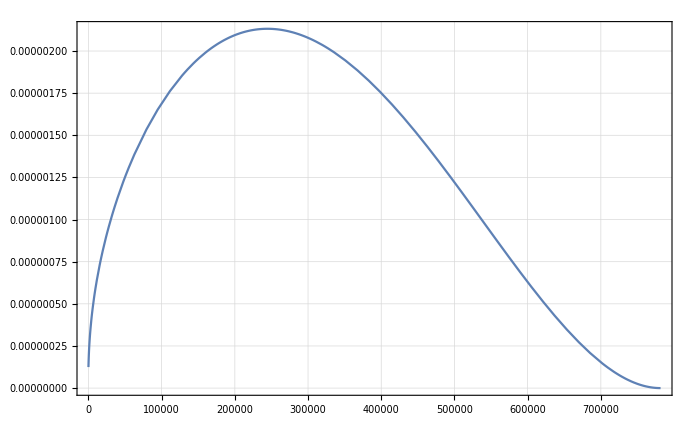

```mathematica
Plot[PDF[ElectronSpectrumPDF,me+T],{T,0,E0-me}]
```

```mathematica
NIntegrate[PDF[ElectronSpectrumPDF,me+T],{T,0,E0-me}]
```

1.

```mathematica
ProtonSpectrumPDF=ProbabilityDistribution[wpNormedGlueck[T,λ0,a0,0.],{T,0.,tpMax}]
```

ProbabilityDistribution[8.24116×10^-21 (0.-0.11175 (1.29333×10^6+1/3 (-1.29333×10^6-(2.6112×10^11)/(1.29333×10^6-43348.9 √x)+43348.9 √x)) (1.29333×10^6+(2.6112×10^11)/(1.29333×10^6-43348.9 √x)-43348.9 √x)^2+0.11175 (1.29333×10^6+1/3 (-1.29333×10^6-(2.6112×10^11)/(1.29333×10^6+43348.9 √x)-43348.9 √x)) (1.29333×10^6+(2.6112×10^11)/(1.29333×10^6+43348.9 √x)+43348.9 √x)^2+4.9797×10^7 (1.29333×10^6+(2.6112×10^11)/(1.29333×10^6-43348.9 √x)-43348.9 √x) (-751.192+x)-4.9797×10^7 (1.29333×10^6+(2.6112×10^11)/(1.29333×10^6+43348.9 √x)+43348.9 √x) (-751.192+x)),{x,0.,751.192}]

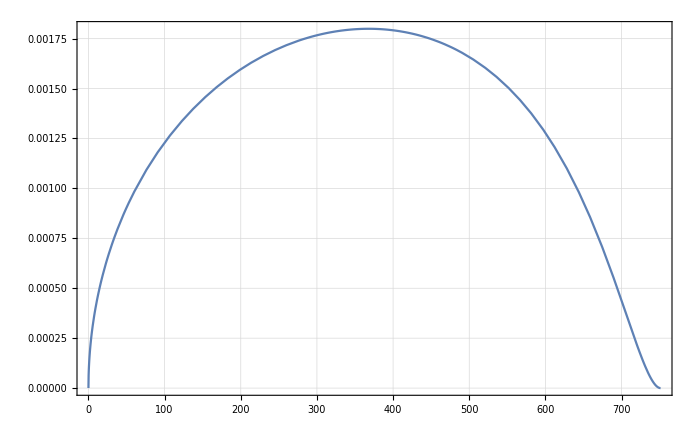

```mathematica
Plot[PDF[ProtonSpectrumPDF,T],{T,0,tpMax}]
```

```mathematica
NIntegrate[PDF[ProtonSpectrumPDF,T],{T,0,tpMax}]
```

1.

## ThetaDist

```mathematica
ThetaMax
```

π/4

```mathematica
ThetaMaxDegree=ThetaMax/Pi*180.
```

45.

```mathematica
ThetaNorm=Integrate[Sin[th/180*Pi],{th,0,ThetaMaxDegree}]
```

16.7815

```mathematica
ThetaPDF=ProbabilityDistribution[Sin[th/180.*Pi],{th,0,ThetaMaxDegree},Method->"Normalize"]
```

ProbabilityDistribution[0.0595893 Sin[0.0174533 x],{x,0,45.}]

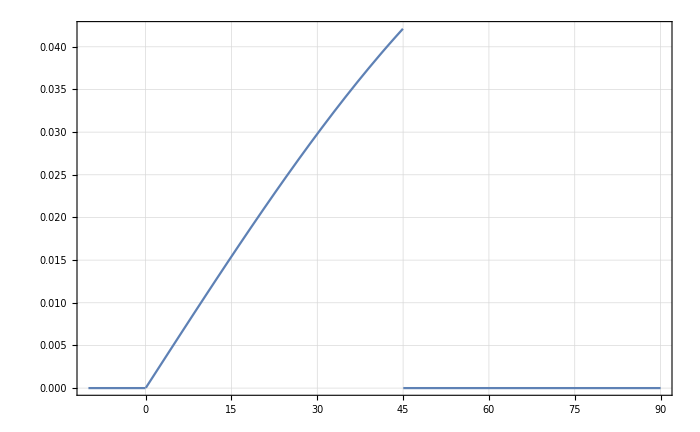

```mathematica
Plot[PDF[ThetaPDF,x],{x,-10,90}]
```

```mathematica
RandomVariate[ThetaPDF,10]
```

{43.1286,43.7714,36.8317,24.6372,31.5194,29.2924,38.3246,34.9961,43.7911,32.6305}

```mathematica
testdata=RandomVariate[ThetaPDF,10^4];
```

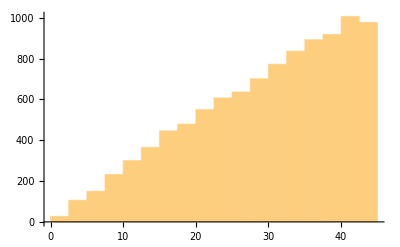

```mathematica
Histogram[testdata,{0,45,2.5}]
```

## Phi Uniform

```mathematica
PhiPDF=UniformDistribution[{0,2Pi}]
```

UniformDistribution[{0,2 π}]

## create data

## electron energy also in eV

```mathematica
EeList=ParallelTable[RandomVariate[ElectronSpectrumPDF,PackageSize]-me,{DataSets}];
```

### we can also load from dump save

```mathematica
SetDirectory[DumpLoadDir]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_5e7_1e4

```mathematica
ClearAll[EeList]
```

```mathematica
Get["EeList.mx"]
```

```mathematica
EeList//Dimensions
```

{5000,10000}

```mathematica
EeList=Map[Partition[#,PackageSize]&,EeList];
```

```mathematica
EeList//Dimensions
```

{5000,5,2000}

```mathematica
EeList=Flatten[EeList,1];
```

```mathematica
EeList//Dimensions
```

{25000,2000}

### proton Ekin

```mathematica
TpList=ParallelTable[RandomVariate[ProtonSpectrumPDF,PackageSize],{DataSets}];
```

### we can also load from dump save

```mathematica
ClearAll[EeList]
```

```mathematica
Get["TpList.mx"]
```

```mathematica
TpList//Dimensions
```

{5000,10000}

```mathematica
TpList=Map[Partition[#,PackageSize]&,TpList];
```

```mathematica
TpList//Dimensions
```

{5000,5,2000}

```mathematica
TpList=Flatten[TpList,1];
```

```mathematica
TpList//Dimensions
```

{25000,2000}

## Theta

```mathematica
CloseKernels[]
```

{KernelObject[1,local,<defunct>],KernelObject[2,local,<defunct>],KernelObject[3,local,<defunct>]}

```mathematica
LaunchKernels[4]
```

{KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local]}

```mathematica
ClearAll[ThetaList]
```

```mathematica
ThetaList=ParallelTable[RandomVariate[ThetaPDF,PackageSize],{DataSets}];
```

### takes 1513s for 3 cores,

### we can also load from dump save

```mathematica
ClearAll[ThetaList]
```

```mathematica
Get["ThetaList.mx"]
```

Get::noopen: Cannot open ThetaList.mx.

$Failed

```mathematica
ThetaList//Dimensions
```

{25000,2000}

```mathematica
ThetaList=Map[Partition[#,PackageSize]&,ThetaList];
```

```mathematica
ThetaList//Dimensions
```

{5000,5,2000}

```mathematica
ThetaList=Flatten[ThetaList,1];
```

```mathematica
ThetaList//Dimensions
```

{25000,2000}

## Phi

```mathematica
PhiList=ParallelTable[RandomVariate[PhiPDF,PackageSize]/Pi*180.,{DataSets}];
```

### we can also load from dump save

```mathematica
ClearAll[EeList]
```

```mathematica
Get["PhiList.mx"]
```

```mathematica
PhiList//Dimensions
```

{5000,10000}

```mathematica
PhiList=Map[Partition[#,PackageSize]&,PhiList];
```

```mathematica
PhiList//Dimensions
```

{5000,5,2000}

```mathematica
PhiList=Flatten[PhiList,1];
```

```mathematica
PhiList//Dimensions
```

{25000,2000}

## data check

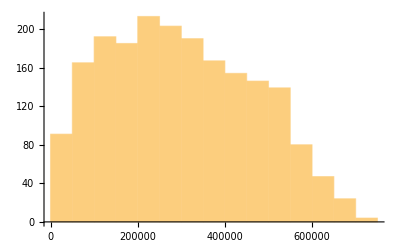

```mathematica
Histogram[EeList[[1]]]
```

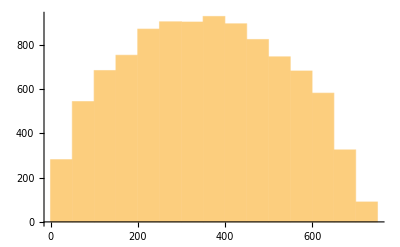

```mathematica
Histogram[TpList[[1]]]
```

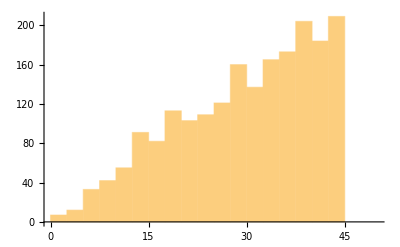

```mathematica
Histogram[ThetaList[[1]],{0,50,2.5}]
```

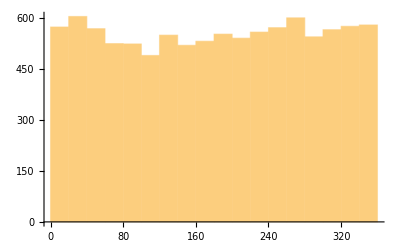

```mathematica
Histogram[PhiList[[1]]]
```

## export

```mathematica
Which[PackageSize==10^4,PackageString="1e4_",PackageSize==2*10^3,PackageString="2e3_"]
```

2e3_

```mathematica
DataSets
```

25000

```mathematica
Table[
Export["Spectra"<>PackageString<>ToString[i-1]<>".txt",Transpose[{SetPrecision[ThetaList[[i]],10],SetPrecision[PhiList[[i]],10],SetPrecision[EeList[[i]],10],SetPrecision[TpList[[i]],10]}],"Table"],
{i,DataSets}];
```

### takes 2726s for 5e7_2e3

```mathematica
Directory[]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_5e7_2e3

## DumpSaving

```mathematica
DumpSaveDir
```

~/FerencSource+Spectra/Mma_Spectra_5e7_1e4

```mathematica
SetDirectory[DumpSaveDir]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_5e7_1e4

```mathematica
DumpSave["EeList.mx",EeList]
```

{{1}}
 |  |  |  |

```mathematica
DumpSave["TpList.mx",TpList]
```

{{{444.223,401.612,399.035,506.698,201.26,346.285,362.473,381.024,570.812,22.4877,271.12,240.589,710.553,422.823,698.011,395.304,341.594,199.36,190.437,9962,512.812,502.116,401.38,195.308,119.572,414.353,275.447,667.206,74.5117,325.885,267.131,593.809,315.631,425.268,128.01,307.889,254.109,328.805,590.825},4999}}
 |  |  |  |

```mathematica
DumpSave["ThetaList.mx",ThetaList]
```

{{1}}
 |  |  |  |

```mathematica
DumpSave["PhiList.mx",PhiList]
```

{{1}}
 |  |  |  |